```mathematica
Needs["Quantum`Notation`"];
```

```mathematica
SetQuantumAliases[]
```

ALIASES:
[ESC]ket[ESC]        ket template
[ESC]bra[ESC]        bra template
[ESC]braket[ESC]     braket template
[ESC]op[ESC]         operator template
[ESC].[ESC]          quantum concatenation infix symbol
[ESC]on[ESC]         quantum concatenation infix symbol
[ESC]tp[ESC]         tensor product infix symbol
[ESC]qp[ESC]         quantum product template
[ESC]qs[ESC]         sigma notation for sums template
[ESC]si[ESC]         sigma notation for sums template
[ESC]ev[ESC]         eigenvalue-label template
[ESC]eket[ESC]       eigenstate template
[ESC]eeket[ESC]      two-operators-eigenstate template
[ESC]eeeket[ESC]     three-operators-eigentstate template
[ESC]ebra[ESC]       bra of eigenstate template
[ESC]eebra[ESC]      bra of two-operators-eigenstate template
[ESC]eeebra[ESC]     bra of three-operators-eigentstate template
[ESC]ebraket[ESC]    braket of eigenstates template
[ESC]eebraket[ESC]   braket of two-operators-eigenstates template
[ESC]eeebraket[ESC]  braket of three-operators-eigentstate template
[ESC]ketbra[ESC]     operator (matrix) element template
[ESC]eketbra[ESC]    operator (matrix) element template
[ESC]eeketbra[ESC]   operator (matrix) element template
[ESC]eeeketbra[ESC]  operator (matrix) element template
[ESC]her[ESC]        hermitian conjugate template
[ESC]con[ESC]        complex conjugate template
[ESC]norm[ESC]       quantum norm template
[ESC]trace[ESC]      partial trace template
[ESC]comm[ESC]       commutator template
[ESC]anti[ESC]       anticommutator template
[ESC]su[ESC]         subscript template
[ESC]po[ESC]         power template

The quantum concatenation infix symbol [ESC]on[ESC] is used for operator application, inner product and outer product.

SetQuantumAliases[] must be executed again in each new notebook that is created, only one time per notebook.

```mathematica
SetQuantumObject[σ,σx,σy,σz,c];
```

```mathematica
Do[⟦SuperDagger[σ[i]],σ[j]⟧_-=2*σz[i]*KroneckerDelta[i,j],{i,0,3},{j,0,3}]
```

```mathematica
Do[⟦SuperDagger[σ[i]],SuperDagger[σ[j]]⟧_-=0,{i,0,3},{j,0,3}]
```

```mathematica
Do[⟦σ[i],σ[j]⟧_-=0,{i,0,3},{j,0,3}]
```

```mathematica
Do[⟦σx[i],σx[j]⟧_-=0,{i,0,3},{j,0,3}]
```

```mathematica
Do[⟦σy[i],σy[j]⟧_-=0,{i,0,3},{j,0,3}]
```

```mathematica
Do[⟦σz[i],σz[j]⟧_-=0,{i,0,3},{j,0,3}]
```

```mathematica
Do[⟦σx[i],σy[j]⟧_-=2*I*σz[i]*KroneckerDelta[i,j],{i,0,3},{j,0,3}]
```

```mathematica
Do[σx[i]·σx[i]=1,{i,0,3}]
```

```mathematica
Do[σy[i]·σy[i]=1,{i,0,3}]
```

```mathematica
Do[σz[i]·σz[i]=1,{i,0,3}]
```

```mathematica
Do[⟦σz[i],SuperDagger[σ[j]]⟧_-=2*SuperDagger[σ[i]]*KroneckerDelta[i,j],{i,0,3},{j,0,3}]
```

```mathematica
Do[⟦σz[i],σ[j]⟧_-=-2*σ[i]*KroneckerDelta[i,j],{i,0,3},{j,0,3}]
```

```mathematica
Do[SuperDagger[σ[i]]·σz[i]=-SuperDagger[σ[i]],{i,0,3}]
```

```mathematica
Do[σz[i]·SuperDagger[σ[i]]=SuperDagger[σ[i]],{i,0,3}]
```

```mathematica
Do[σ[i]·σz[i]=σ[i],{i,0,3}]
```

```mathematica
Do[σz[i]·σ[i]=-σ[i],{i,0,3}]
```

```mathematica
c2σ=Flatten@{Table[c[i]->zz075NonCommutativeTimes@@Flatten@{σ[i],(-σz/@Reverse@Range[0,i-1])},{i,0,3}],Table[SuperDagger[c[i]]->zz075NonCommutativeTimes@@Flatten@{SuperDagger[σ[i]],(-σz/@Reverse@Range[0,i-1])},{i,0,3}]}
```

{c[0]→σ[0],c[1]→-σz[0]·σ[1],c[2]→σz[0]·σz[1]·σ[2],c[3]→-σz[0]·σz[1]·σz[2]·σ[3],c[0]^†→σ[0]^†,c[1]^†→-σz[0]·σ[1]^†,c[2]^†→σz[0]·σz[1]·σ[2]^†,c[3]^†→-σz[0]·σz[1]·σz[2]·σ[3]^†}

```mathematica
σ2=Flatten@{Table[σ[i]->(σx[i]+I*σy[i])/2,{i,0,1}],Table[SuperDagger[σ[i]]->(σx[i]-I*σy[i])/2,{i,0,1}]}
```

{σ[0]→1/2 (σx[0]+ⅈ σy[0]),σ[1]→1/2 (σx[1]+ⅈ σy[1]),σ[0]^†→1/2 (σx[0]-ⅈ σy[0]),σ[1]^†→1/2 (σx[1]-ⅈ σy[1])}

```mathematica
SuperDagger[c[0]]·c[0]/.c2σ
```

σ[0]^†·σ[0]

```mathematica
SuperDagger[c[0]]·c[1]/.c2σ
```

σ[0]^†·σ[1]

```mathematica
CommutatorExpand[SuperDagger[c[1]]·c[0]/.c2σ]
```

σ[1]^†·σ[0]

```mathematica
CommutatorExpand[c[0]·c[1]/.c2σ]
```

-σ[0]·σ[1]

```mathematica
CommutatorExpand[SuperDagger[c[1]]·SuperDagger[c[0]]/.c2σ]
```

-σ[0]^†·σ[1]^†

```mathematica
cc2σ={SuperDagger[c[0]]·c[1]-> (SuperDagger[c[0]]·c[1]/.c2σ),SuperDagger[c[1]]·c[0]-> CommutatorExpand[SuperDagger[c[1]]·c[0]/.c2σ],c[0]·c[1]->CommutatorExpand[c[0]·c[1]/.c2σ], SuperDagger[c[1]]·SuperDagger[c[0]]-> CommutatorExpand[SuperDagger[c[1]]·SuperDagger[c[0]]/.c2σ],SuperDagger[c[0]]·c[0]->( σz[0]+1)/2}
```

{c[0]^†·c[1]→σ[0]^†·σ[1],c[1]^†·c[0]→σ[1]^†·σ[0],c[0]·c[1]→-σ[0]·σ[1],c[1]^†·c[0]^†→-σ[0]^†·σ[1]^†,c[0]^†·c[0]→1/2 (1+σz[0])}

```mathematica
CommutatorExpand[t*(SuperDagger[c[0]]·c[1]+SuperDagger[c[1]]·c[0])+Δ*(c[0]·c[1]+SuperDagger[c[1]]·SuperDagger[c[0]])/.cc2σ/.σ2]//Simplify
```

1/2 ((t-Δ) σx[0]·σx[1]+(t+Δ) σy[0]·σy[1])

```mathematica
CommutatorExpand[-μ*SuperDagger[c[0]]·c[0]/.cc2σ/.σ2]//Simplify
```

-1/2 μ (1+σz[0])

### NW

```mathematica
H=KroneckerProduct[PauliMatrix[3],((-2*t*Cos[k]+2*t-μ)*PauliMatrix[0]+Vz*PauliMatrix[1])+2*α*Sin[k]*PauliMatrix[2]]+Δ*KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]
```

{{2 t-μ-2 t Cos[k],Vz-2 ⅈ α Sin[k],0,-Δ},{Vz+2 ⅈ α Sin[k],2 t-μ-2 t Cos[k],Δ,0},{0,Δ,-2 t+μ+2 t Cos[k],-Vz+2 ⅈ α Sin[k]},{-Δ,0,-Vz-2 ⅈ α Sin[k],-2 t+μ+2 t Cos[k]}}

```mathematica
H//MatrixForm
```

(2 t-μ-2 t Cos[k] | Vz-2 ⅈ α Sin[k] | 0 | -Δ
Vz+2 ⅈ α Sin[k] | 2 t-μ-2 t Cos[k] | Δ | 0
0 | Δ | -2 t+μ+2 t Cos[k] | -Vz+2 ⅈ α Sin[k]
-Δ | 0 | -Vz-2 ⅈ α Sin[k] | -2 t+μ+2 t Cos[k])

```mathematica
Eigenvalues[H/.{t->1,α->1,μ->1,Δ->1,Vz->2,k->1.}]
```

{-3.44397,3.44397,1.95363,-1.95363}

```mathematica
Eigenvalues[H/.{t->1,α->1,μ->1,Δ->1,Vz->2,k->-1.}]
```

{-3.44397,3.44397,1.95363,-1.95363}

```mathematica
Transpose@Block[{t=1,α=1,μ=1,Δ=1,Vz=2},Table[Eigenvalues[H],{k,Range[-1,1,0.05]*π}]]
```

{{-5.16228,4.84411,-4.49339,-4.12415,-3.75519,-3.41421,3.14492,-3.0079,3.03957,-3.19955,-3.41421,-3.63082,-3.81957,3.96369,-4.05354,4.08402,-4.05354,3.96369,-3.81957,-3.63082,-3.41421,-3.19955,-3.03957,-3.0079,-3.14492,-3.41421,-3.75519,4.12415,4.49339,-4.84411,-5.16228,5.43694,-5.65943,-5.8231,-5.92319,5.95687,-5.92319,5.8231,-5.65943,5.43694,5.16228},{5.16228,-4.84411,4.49339,4.12415,3.75519,3.41421,-3.14492,3.0079,-3.03957,3.19955,3.41421,3.63082,3.81957,-3.96369,4.05354,-4.08402,4.05354,-3.96369,3.81957,3.63082,3.41421,3.19955,3.03957,3.0079,3.14492,3.41421,3.75519,-4.12415,-4.49339,4.84411,5.16228,-5.43694,5.65943,5.8231,5.92319,-5.95687,5.92319,-5.8231,5.65943,-5.43694,-5.16228},{-1.16228,0.844108,0.493395,0.124146,-0.244807,0.585786,0.855078,0.992097,-0.960432,0.800452,-0.585786,-0.369179,-0.180427,-0.0363096,-0.0535377,-0.0840215,-0.0535377,-0.0363096,-0.180427,-0.369179,-0.585786,0.800452,-0.960432,-0.992097,0.855078,0.585786,-0.244807,0.124146,0.493395,0.844108,-1.16228,1.43694,1.65943,1.8231,1.92319,-1.95687,1.92319,1.8231,1.65943,-1.43694,1.16228},{1.16228,-0.844108,-0.493395,-0.124146,0.244807,-0.585786,-0.855078,-0.992097,0.960432,-0.800452,0.585786,0.369179,0.180427,0.0363096,0.0535377,0.0840215,0.0535377,0.0363096,0.180427,0.369179,0.585786,-0.800452,0.960432,0.992097,-0.855078,-0.585786,0.244807,-0.124146,-0.493395,-0.844108,1.16228,-1.43694,-1.65943,-1.8231,-1.92319,1.95687,-1.92319,-1.8231,-1.65943,1.43694,-1.16228}}

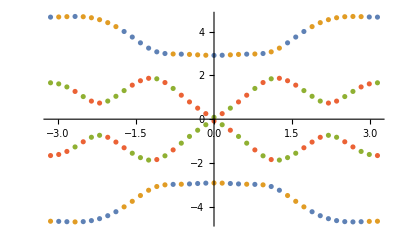

```mathematica
ListPlot[Transpose@Block[{t=1,α=1,μ=1,Δ=1,Vz=1.5},Table[Eigenvalues[H],{k,Range[-1,1,0.05]*π}]],DataRange->{-π,π}]
```

```mathematica
Eigensystem[H/.k->0]
```

{{-Vz-√(Δ^2+μ^2),Vz-√(Δ^2+μ^2),-Vz+√(Δ^2+μ^2),Vz+√(Δ^2+μ^2)},{{-(-μ-√(Δ^2+μ^2))/Δ,-(μ+√(Δ^2+μ^2))/Δ,1,1},{-(-μ-√(Δ^2+μ^2))/Δ,-(-μ-√(Δ^2+μ^2))/Δ,-1,1},{-(-μ+√(Δ^2+μ^2))/Δ,-(μ-√(Δ^2+μ^2))/Δ,1,1},{-(-μ+√(Δ^2+μ^2))/Δ,-(-μ+√(Δ^2+μ^2))/Δ,-1,1}}}

### NW Jordan-Wigner

```mathematica
SetQuantumObject[σ,c];
```

```mathematica
Do[⟦σ[i,"+"],σ[j,"-"]⟧_-=2*σ[i,"z"]*KroneckerDelta[i,j],{i,0,3},{j,0,3}]
```

```mathematica
Do[⟦σ[i,s],σ[j,s]⟧_-=0,{i,0,3},{j,0,3},{s,{"+","-","x","y","z"}}]
```

```mathematica
Do[σ[i,s]·σ[i,s]=1,{i,0,3},{s,{"x","y","z"}}]
```

```mathematica
Do[σ[i,s]·σ[i,s]=0,{i,0,3},{s,{"+","-"}}]
```

```mathematica
Do[⟦σ[i,"z"],σ[j,"+"]⟧_-=2*σ[i,"+"]*KroneckerDelta[i,j],{i,0,3},{j,0,3}]
```

```mathematica
Do[⟦σ[i,"z"],σ[j,"-"]⟧_-=-2*σ[i,"-"]*KroneckerDelta[i,j],{i,0,3},{j,0,3}]
```

```mathematica
Do[σ[i,s]·σ[i,"z"]=If[s=="+",-1,1]*σ[i,s],{i,0,3},{s,{"-","+"}}]
```

```mathematica
Do[σ[i,"z"]·σ[i,s]=If[s=="+",1,-1]*σ[i,s],{i,0,3},{s,{"-","+"}}]
```

```mathematica
c2σ=Flatten@{Table[c[i]->zz075NonCommutativeTimes@@Flatten@{σ[i,"-"],(-σ[#,"z"]&/@Reverse@Range[0,i-1])},{i,0,3}],Table[SuperDagger[c[i]]->zz075NonCommutativeTimes@@Flatten@{σ[i,"+"],(-σ[#,"z"]&/@Reverse@Range[0,i-1])},{i,0,3}]}
```

{c[0]→σ[0,-],c[1]→-σ[0,z]·σ[1,-],c[2]→σ[0,z]·σ[1,z]·σ[2,-],c[3]→-σ[0,z]·σ[1,z]·σ[2,z]·σ[3,-],c[0]^†→σ[0,+],c[1]^†→-σ[0,z]·σ[1,+],c[2]^†→σ[0,z]·σ[1,z]·σ[2,+],c[3]^†→-σ[0,z]·σ[1,z]·σ[2,z]·σ[3,+]}

```mathematica
cc2σ=Table[SuperDagger[c[i]]·c[i]->(σ[i,"z"]+1)/2,{i,0,3}]
```

{c[0]^†·c[0]→1/2 (1+σ[0,z]),c[1]^†·c[1]→1/2 (1+σ[1,z]),c[2]^†·c[2]→1/2 (1+σ[2,z]),c[3]^†·c[3]→1/2 (1+σ[3,z])}

```mathematica
σ2=Flatten@{Table[σ[i,"-"]->(σ[i,"x"]+I*σ[i,"y"])/2,{i,0,3}],Table[σ[i,"+"]->(σ[i,"x"]-I*σ[i,"y"])/2,{i,0,3}]}
```

{σ[0,-]→1/2 (σ[0,x]+ⅈ σ[0,y]),σ[1,-]→1/2 (σ[1,x]+ⅈ σ[1,y]),σ[2,-]→1/2 (σ[2,x]+ⅈ σ[2,y]),σ[3,-]→1/2 (σ[3,x]+ⅈ σ[3,y]),σ[0,+]→1/2 (σ[0,x]-ⅈ σ[0,y]),σ[1,+]→1/2 (σ[1,x]-ⅈ σ[1,y]),σ[2,+]→1/2 (σ[2,x]-ⅈ σ[2,y]),σ[3,+]→1/2 (σ[3,x]-ⅈ σ[3,y])}

#### c[i]^†c[i+1]+h.c.

```mathematica
Simplify/@CommutatorExpand[SuperDagger[c[0]]·c[2]+SuperDagger[c[1]]·c[3]+SuperDagger[c[3]]·c[1]+SuperDagger[c[2]]·c[0]/.c2σ]
```

-σ[0,+]·σ[1,z]·σ[2,-]-σ[0,-]·σ[1,z]·σ[2,+]-σ[1,+]·σ[2,z]·σ[3,-]-σ[1,-]·σ[2,z]·σ[3,+]

#### c[i]^†c[i]

```mathematica
CommutatorExpand[SuperDagger[c[0]]·c[0]+SuperDagger[c[1]]·c[1]/.cc2σ/.c2σ]//Simplify
```

1/2 (2+σ[0,z]+σ[1,z])

#### c[i]^†(iσ_y)c[i+1]+h.c.

```mathematica
Simplify/@CommutatorExpand[SuperDagger[c[0]]·c[3]-SuperDagger[c[1]]·c[2]+SuperDagger[(SuperDagger[c[0]]·c[3]-SuperDagger[c[1]]·c[2])]/.cc2σ/.c2σ]
```

-σ[1,+]·σ[2,-]-σ[1,-]·σ[2,+]+σ[0,+]·σ[1,z]·σ[2,z]·σ[3,-]+σ[0,-]·σ[1,z]·σ[2,z]·σ[3,+]

#### c[i]^†σ_x c[i]

```mathematica
CommutatorExpand[SuperDagger[c[0]]·c[1]+SuperDagger[c[1]]·c[0]/.cc2σ/.c2σ]
```

σ[0,+]·σ[1,-]+σ[0,-]·σ[1,+]

#### c[i,up]c[i,down]+h.c.

```mathematica
CommutatorExpand[c[0]·c[1]+SuperDagger[c[1]]·SuperDagger[c[0]]/.cc2σ/.c2σ]
```

-σ[0,-]·σ[1,-]-σ[0,+]·σ[1,+]

#### -t*(c[i]^†c[i+1]+h.c.)

```mathematica
-t*(Simplify/@CommutatorExpand[SuperDagger[c[0]]·c[2]+SuperDagger[c[1]]·c[3]+SuperDagger[c[3]]·c[1]+SuperDagger[c[2]]·c[0]/.c2σ]/.σ2)//Simplify
```

1/2 t (σ[0,x]·σ[1,z]·σ[2,x]+σ[0,y]·σ[1,z]·σ[2,y]+σ[1,x]·σ[2,z]·σ[3,x]+σ[1,y]·σ[2,z]·σ[3,y])

#### -α*(c[i]^†(iσ_y)c[i+1]+h.c.)

```mathematica
-α(Simplify/@CommutatorExpand[SuperDagger[c[0]]·c[3]-SuperDagger[c[1]]·c[2]+SuperDagger[(SuperDagger[c[0]]·c[3]-SuperDagger[c[1]]·c[2])]/.cc2σ/.c2σ]/.σ2)//Simplify
```

1/2 α (σ[1,x]·σ[2,x]+σ[1,y]·σ[2,y]-σ[0,x]·σ[1,z]·σ[2,z]·σ[3,x]-σ[0,y]·σ[1,z]·σ[2,z]·σ[3,y])

#### Vz*c[i]^†σ_x c[i]+Δ(c[i,up]c[i,down]+h.c.)

```mathematica
CommutatorExpand[Vz*(SuperDagger[c[0]]·c[1]+SuperDagger[c[1]]·c[0])+Δ*(c[0]·c[1]+SuperDagger[c[1]]·SuperDagger[c[0]])/.c2σ]/.σ2//Simplify
```

1/2 ((Vz-Δ) σ[1,x]·σ[0,x]+(Vz+Δ) σ[1,y]·σ[0,y])

```mathematica
CommutatorExpand[c[0]·c[1]+SuperDagger[c[1]]·SuperDagger[c[0]]/.cc2σ/.c2σ]/.σ2//Simplify
```

1/2 (-σ[1,x]·σ[0,x]+σ[1,y]·σ[0,y])